```mathematica
(*1*)
X={{1,2, 0},{-1,1,0},{0,1,2}};
Y={3,1,3};
LinearSolve[X,Y]
```

{1/3,4/3,5/6}

```mathematica
(*2*)
A = x-2y+3z==1
B = 2x+3y-z==5
Solve[A && B,{x,y}]
```

x-2 y+3 z==1

2 x+3 y-z==5

{{x→13/7-z,y→1/7 (3+7 z)}}

```mathematica
(*3*)
Limit[ⅇ^x/(x^3-x+2),x->Infinity]
```

∞

```mathematica
Limit[ⅇ^(1/(x^2-1)),x->1,Direction->"FromAbove"]
```

∞

```mathematica
Limit[ⅇ^(1/(x^2-1)),x->1,Direction->"FromBelow"]
```

0

```mathematica
Integrate[Sin[x]/x,{x,0,Infinity}]
```

π/2

```mathematica
(*4*)
DSolve[y'[x]==y[x]*x,y[x],x]
```

```mathematica
{{y[x]->ⅇ^(x^2/2) C[1]}}
```

{{y[x]→ⅇ^(x^2/2) C[1]}}

```mathematica
(*5*)
DSolve[{y'[x]==y[x]*x,y[1]==2},y[x],x]/.x->7/2
```

```mathematica
{{y[7/2]->2 ⅇ^(45/8)}}
(*6*)
Clear[y];
rr =2 D[y[x,t],x]+D[y[x,t],t];
solution = DSolve[{rr==0,y[0,t]==Cos[t]},y[x,t],{x,t}]
```

```mathematica
{{y[x,t]->Cos[1/2 (2 t-x)]}}
f[x_,t_]=y[x,t]/.solution⟦1⟧;
Plot3D[f[x,t],{x,0,3},{t,-1,4}, PlotStyle->Gray]
```

{{y[x,t]→Cos[1/2 (2 t-x)]}}

```mathematica
-Graphics3D-
(*7*)
```

```mathematica
f[x_]:=Sum[x^i/i!,{i,0,5}] ;
f[x]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120

```mathematica
f[2]
```

109/15

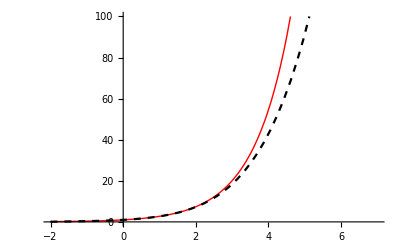

```mathematica
Show[Plot[ⅇ^x,{x,-2,7}, PlotRange->{0,100},PlotStyle->{Red,Thick}],Plot[f[x],{x,-2,7}, PlotRange->{0,100},PlotStyle->{Black,Dashed}]]
```

```mathematica
(*8*)
```

```mathematica
okrag = Graphics[{Pink,Thick,Circle[{5,5},2]}];
kolo = Graphics[{Pink,Disk[{-1,3},1]}];
```

```mathematica
strzalka = Graphics[{Black,Thick, Arrowheads[0.2],Arrow[{{2,1},{2,3}}]}];
```

```mathematica
linia = Graphics[{Pink,Line[{{1,5},{3,1},{0,2}}]}];
```

```mathematica
prostokat = Graphics[{Red,Rectangle[{-1,-3},{-3,-4}]}];
```

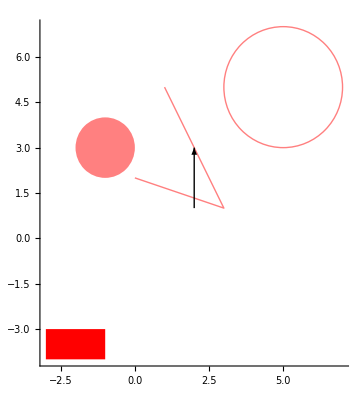

```mathematica
Show[okrag,kolo,linia,strzalka,prostokat, Axes->True]
```